```mathematica
<<CustomTicks`
```

```mathematica
tickll=LogTicks[-20,10];
Do[tickll[[i,1]]=10^tickll[[i,1]],{i,1,Length[tickll]}];
tickll;
```

```mathematica
mass={200,300,500,1000,2000,3000,4000,5000,6000,7000,8000,9000};
massZax={200,300,500,(*700,800,*)900,950,970,1000,1100,1200,1500,2000,3000,4000,5000,6000,7000,8000,9000};
```

## Axion production process

#### input data

```mathematica
xsmumu2mumuax={8.1*10^-9+2*1.24*10^-11,8.7*10^-9+2*7.73*10^-11+1.3*10^-11,9.22*10^-9+2*1.65*10^-10+5.8*10^-11,9.27*10^-9+2*2.64*10^-10+1.47*10^-10,7.29*10^-9+2*2.7*10^-10+1.98*10^-10,5.32*10^-9+2*2.22*10^-10+1.82*10^-10,3.8*10^-9+2*1.7*10^-10+1.49*10^-10,2.65*10^-9+2*1.24*10^-11+8.23*10^-11,1.79*10^-9,1.25*10^-9,6.7*10^-10+2*3.43*10^-11+3.4*10^-11,3.04*10^-10+2*1.58*10^-11+1.6*10^-11}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100(*rescale fa from 1TeV to 10TeV*);
xsmumu2vmvmax={4.63*10^-9(*5.8*10^-11*),5.55*10^-9,6.1*10^-9,5.79*10^-9,4.1*10^-9,2.76*10^-9,1.7*10^-9,9.77*10^-10,4.9*10^-10,1.99*10^-10,5.5*10^-11,5.94*10^-12}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
xsmumu2zax={1.58*10^-10,3.8*10^-10,9.5*10^-10,(*1.6*10^-9(*700GeV*),1.93*10^-9(*800GeV*),*)2.25*10^-9(*900GeV*),2.41*10^-9(*950GeV*),2.476*10^-9(*970GeV*),2.51*10^-9,2.55*10^-9(*1100GeV*),2.54*10^-9(*1200GeV*),2.48*10^-9(*1500GeV*), 2.3*10^-9,2.0*10^-9,1.6*10^-9,1.1*10^-9,7*10^-10,3.5*10^-10,1.2*10^-10,1.8*10^-11}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),(*0.97/(2.17*10^-3),0.97/(2.17*10^-3),*)0.97/(2.17*10^-3),0.97/(2.17*10^-3),0.97/(2.17*10^-3),0.97/(2.165*10^-3),0.97/(2.16*10^-3),0.97/(2.16*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
xswa2wax(*include wz2wax*)=2*(*conjugate*){7.28*10^-10+1.64*10^-10,8.06*10^-10+2.04*10^-10, 8.01*10^-10+2.18*10^-10,7.36*10^-10+2.18*10^-10,5.65*10^-10+1.87*10^-10,4.18*10^-10+1.47*10^-10,3.03*10^-10+1.1*10^-10,2.12*10^-10+7.75*10^-11,1.39*10^-10+5.17*10^-11,8.4*10^-11+3.12*10^-11,4.25*10^-11+1.58*10^-11,1.27*10^-11+4.7*10^-12}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
xsww2zax={5.25*10^-10,6.32*10^-10,6.6*10^-10,6.5*10^-10, 5.08*10^-10,3.56*10^-10,2.28*10^-10,1.3*10^-10,6.3*10^-11,2.4*10^-11,5.46*10^-12,3.6*10^-13}*{0.997/(2.22*10^-3),0.981/(2.2*10^-3),0.97/(2.17*10^-3),0.97/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.16*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3),0.969/(2.157*10^-3)}/100;
(*xsVBF=xsmumu2mumuax+xsmumu2vmvmax;*)

xsmumu2mumuaxdata=Table[{mass[[i]],xsmumu2mumuax[[i]]},{i,1,Length[mass]}];
xsmumu2vmvmaxdata=Table[{mass[[i]],xsmumu2vmvmax[[i]]},{i,1,Length[mass]}];
xsmumu2Vaxdata=Table[{massZax[[i]],xsmumu2zax[[i]]},{i,1,Length[massZax]}];
xswa2waxdata=Table[{mass[[i]],xswa2wax[[i]]},{i,1,Length[mass]}];
xsww2zaxdata=Table[{mass[[i]],xsww2zax[[i]]},{i,1,Length[mass]}];
```

#### plot

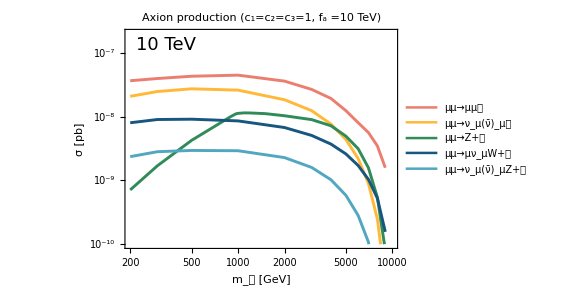

```mathematica
xsplot=ListLogLogPlot[{xsmumu2mumuaxdata,xsmumu2vmvmaxdata,xsmumu2Vaxdata,xswa2waxdata,xsww2zaxdata},Joined->True,PlotRange->{{2*10^2,10^4},{10^-10,2*10^-7}},PlotStyle->{{ColorData[24][1],Thickness[0.005]},{ColorData[24][2],Thickness[0.005]},{RGBColor[0.1875,0.54687,0.347656,1],Thickness[0.005]},{ColorData[24][7],Thickness[0.005]},{ColorData[24][5],Thickness[0.005]}},PlotLabel->Style["Axion production (c_1=c_2=c_3=1, f_a =10 TeV)",Black,18,FontFamily->"Times"],Frame->True,FrameTicks->{{tickll,Automatic},{Automatic,Automatic}},FrameTicksStyle->Directive[Black,15,FontFamily->"Times"],FrameLabel->{Style["m_(|01d44e) [GeV]",Black,18,FontFamily->"Times"],Style["σ [pb]",Black,18,FontFamily->"Times"]},PlotLegends->{Placed[LineLegend[{Style["μμ→μμ𝑎",Black,15,FontFamily->"Times"],Style["μμ→ν_μ(ν̄)_μ𝑎",Black,15,FontFamily->"Times"],Style["μμ→Z+𝑎",Black,15,FontFamily->"Times"],Style["μμ→μν_μW+𝑎",Black,15,FontFamily->"Times"],Style["μμ→ν_μ(ν̄)_μZ+𝑎",Black,15,FontFamily->"Times"]},LegendLayout->{"Row",2}],{{0.01,0.09},{0.0,0.3}}]},Epilog->{Text[Style["10 TeV",Black,18,FontFamily->"Times"],Scaled[{0.04,0.93}],Left,{1,0}]},AspectRatio->0.7,ImageSize->420]
```